# Roberson’s sheath model

http://dx.doi.org/10.1088/0741-3335/55/9/093001

## Fluid model

```mathematica
L=130;
dx=0.5;
R= 0.54/L
α=R^2
```

0.00415385

0.0000172544

```mathematica
s=NDSolve[{{ϕ'[x]==-e[x],e'[x]==(R x)/u[x]-Exp[ϕ[x]],u'[x]==e[x]/u[x]-u[x]/x},{ϕ[dx]==-α dx^2,e[dx]==2α dx,u[dx]==(R dx)/(Exp[-α dx^2]+2α)}},{ϕ[x],e[x],u[x]},{x,dx,L},"StartingStepSize"->dx]
```

{{ϕ[x]→InterpolatingFunction[{{0.5, 130.}}, <>][x],e[x]→InterpolatingFunction[{{0.5, 130.}}, <>][x],u[x]→InterpolatingFunction[{{0.5, 130.}}, <>][x]}}

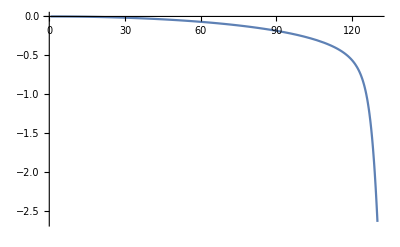

```mathematica
Plot[Evaluate[ϕ[x]/.s],{x,dx,L},PlotRange->All]
```

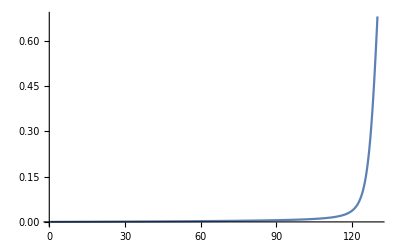

```mathematica
Plot[Evaluate[e[x]/.s],{x,dx,L},PlotRange->All]
```

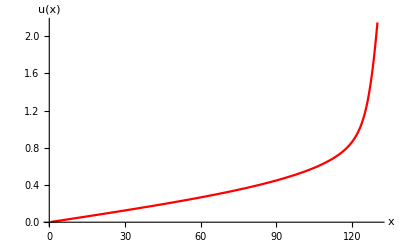

/l/pcagas/repos/students/pcagas/presentations/2016_AIAA/figures/robertson_u.pdf

```mathematica
Plot[Evaluate[u[x]/.s],{x,dx,L},PlotRange->All,PlotStyle->Red,AxesLabel->{x,u[x]},BaseStyle->{FontWeight->"Bold", FontSize->15}]
Export["/l/pcagas/repos/students/pcagas/presentations/2016_AIAA/figures/robertson_u.pdf",%]
```

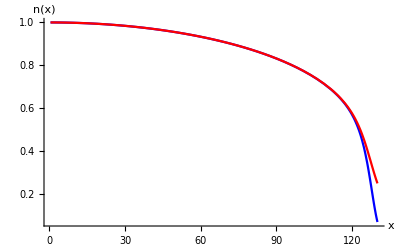

/l/pcagas/repos/students/pcagas/presentations/2016_AIAA/figures/robertson_n.pdf

```mathematica
Subscript[p, 2]=Plot[Evaluate[R x/u[x]/.s],{x,dx,L},PlotRange->All,PlotStyle->Red,AxesLabel->{x,n[x]}, BaseStyle->{FontWeight->"Bold", FontSize->15}];
Subscript[p, 1]=Plot[Evaluate[Exp[ϕ[x]]/.s],{x,dx,L},PlotRange->All,PlotStyle->Blue,AxesLabel->{x,n[x]}, BaseStyle->{FontWeight->"Bold", FontSize->15}];
Show[Subscript[p, 1],Subscript[p, 2]]
Export["/l/pcagas/repos/students/pcagas/presentations/2016_AIAA/figures/robertson_n.pdf",%]
```

## Exporting results

```mathematica
Subscript[m, Elc]=1;
Subscript[m, Ion]=1836.2;
Subscript[T, Elc]=1;
Subscript[T, Ion]=1;
Subscript[u, B]=Sqrt[(Subscript[T, Elc]+Subscript[T, Ion])/Subscript[m, Ion]]
Subscript[v, tElc]=Sqrt[Subscript[T, Elc]/Subscript[m, Elc]]
Subscript[v, tIon]=Sqrt[Subscript[T, Ion]/Subscript[m, Ion]]
numDensityElc=Prepend[Table[Evaluate[Exp[ϕ[x]]/.s],{x,dx, L, dx}],1.0];
numDensityIon=Prepend[Table[Evaluate[R x/u[x]/.s],{x,dx, L, dx}],1.0];
momentumElc=Prepend[Table[Evaluate[Exp[ϕ[x]]u[x] Subscript[u, B]/.s],{x,dx, L, dx}],0.0];
momentumIon=Prepend[Table[Evaluate[R x*Subscript[u, B]/.s],{x,dx, L, dx}],0.0];
energyElc=Prepend[Table[Evaluate[Exp[ϕ[x]]((u[x] Subscript[u, B])^2+Subscript[v, tElc]^2)/.s],{x,dx, L, dx}],Subscript[v, tElc]^2];energyIon=Prepend[Table[Evaluate[R x/u[x]((u[x] Subscript[u, B])^2+Subscript[v, tIon]^2)/.s],{x,dx, L, dx}],Subscript[v, tIon]^2];
```

0.0330031

1

0.0233367

```mathematica
Export["/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initNumDensityElc.txt", Flatten[numDensityElc]]
Export["/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initNumDensityIon.txt", Flatten[numDensityIon]]
Export["/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initMomentumElc.txt", Flatten[momentumElc]]
Export["/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initMomentumIon.txt", Flatten[momentumIon]]
Export["/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initEnergyElc.txt", Flatten[energyElc]]
Export["/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initEnergyIon.txt", Flatten[energyIon]]
```

/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initNumDensityElc.txt

/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initNumDensityIon.txt

/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initMomentumElc.txt

/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initMomentumIon.txt

/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initEnergyElc.txt

/l/pcagas/repos/gkeyll-simulations/pcagas/sheath1D1V/sandbox/initEnergyIon.txt